```mathematica
filesAR=FileNames["/home/carla/GDC/PHI/GDC_Conf_AR_PHI_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/PHI/GDC_Conf_BR_PHI_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]];
confBR=dataBR[[All,1]];
```

```mathematica
dojAR=confAR[[All,1]][[All,1]]
zAR=confAR[[All,2]][[All,1]]
fAR=confAR[[All,3]][[All,1]]
```

{0.000381136,0.00473934,0.030303,0.0104167,0.00157978,0.00473934,1.}

{0.000251975,0.00461743,0.0301736,0.0103899,0.00157685,0.00473642,1.}

{0.49378,0.949845,0.991496,0.994865,0.996293,0.998772,1}

```mathematica
dojBR=confBR[[All,1]][[All,1]]
zBR=confBR[[All,2]][[All,1]]
fBR=confBR[[All,3]][[All,1]]
```

{0.000381136,0.00473934,0.0110063,0.00153818,0.00157978}

{0.000258695,0.00461134,0.0109795,0.00153525,0.00157686}

{0.513716,0.947406,0.995143,0.996193,0.996308}

```mathematica
sList={2,3,4,5,6,7,8};
sList2={2.5,3.5,4.5,5.5,6.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];


dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
zPAR= {#[[2]],#[[1]]}&/@Map[{zAR[[#]],sList[[#]]}&,ran];
fPAR= {#[[2]],#[[1]]}&/@Map[{fAR[[#]],sList[[#]]}&, ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&,ran2];
zPBR= {#[[2]],#[[1]]}&/@Map[{zBR[[#]],sList2[[#]]}&, ran2];
fPBR= {#[[2]],#[[1]]}&/@Map[{fBR[[#]],sList2[[#]]}&,ran2];
```

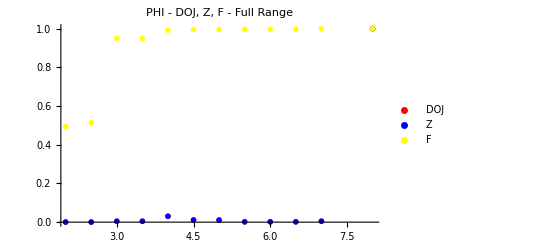

```mathematica
PlotAllParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->All, PlotLabel->"PHI - DOJ, Z, F - Full Range", PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

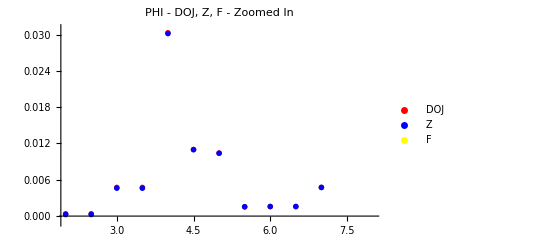

```mathematica
PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{-0.001, 0.031},  PlotLabel->"PHI - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/PHI/"];
(*Put[{confM,{bvE,bvHEK}},filenameOut]*)
Put[Union[dojPAR,dojPBR],"PHI_DOJ.txt"]
Put[Union[zPAR,zPBR],"PHI_Z.txt"]
Put[Union[fPAR,fPBR],"PHI_F.txt"]
Export["PHI_ALL.jpeg",PlotAllParts,ImageSize->850]
Export["PHI_Zoomed_In.jpeg",PlotParts,ImageSize->850]
```

PHI_ALL.jpeg

PHI_Zoomed_In.jpeg

```mathematica
"PHI_ALL.jpeg"
```

PHI_ALL.jpeg

```mathematica
"PHI_Zoomed_In.jpeg"
```

PHI_Zoomed_In.jpeg